```mathematica
ParallelEvaluate[Off[General::munfl,FindFit::cvmit]];
Off[General::munfl,General::stop,LinearSolve::luc,FindFit::cvmit]
SetDirectory[NotebookDirectory[]]
```

/home/johannesk/kette_repo/limit_cycles/src_mathematica/good_fits

```mathematica
LECsNUCL=Import["../LECs_nucl_Joki.dat","Table"][[2;;]];

activeLEC=LECsNUCL[[All,{1,2,3}]];
hbar=197.327053;
Mm=938.92;
m1=2 Mm;m2= Mm;
μ=m1 m2/(m1+m2);
mh2=(2 Mm)/(hbar)^2;
Print[1/mh2]
```

20.7355

```mathematica
I1[lam_,b1_,b2_] :=(Pi^3)/(3^(1/2)(b1^2+b2^2+2b1 b2+((b1 lam^2)/2)+((b2 lam^2)/2))^(3/2));
I2[lam_,b1_,b2_] := (Pi^3)/((3(b1^2+b2^2+2b1 b2+b1 lam^2+ b2 lam^2+(3lam^4/16)))^(3/2));

I1Joki[lam_,b1_,b2_] :=(2 Pi)^3 /(12 ((b1+b2)^2+2 (b1+b2) lam))^(3/2);
I2Joki[lam_,b1_,b2_] := (2 Pi)^3/(12 ((b1+b2)^2+4 lam (b1+b2)+3 lam^2))^(3/2);
I3[b1_,b2_] :=1/(2 3^(1/2)) b1 b2 (2 Pi)^3/(b1+b2)^4;
```

```mathematica
ham[lam_,b1_,b2_,c0_,d1_]:=3 c0 I1Joki[0.25 lam^2,b1,b2]+d1 I2Joki[0.25 lam^2,b1,b2]+(1/mh2) I3[b1,b2];

norm[b1_,b2_]:=(2 Pi)^3/(12^(3/2)(b1+b2)^3);
```

dimD:  bare basis dimension
widths: educated guess for the Gaussian width parameters each of which defines a bare basis function  e^(-β∑(r̄)^2)
lamd: cutoff/regularization parameter of the interaction
evlowthreshold: empirically determined threshold which sets the lower bound for the norm eigenvalues that are allowed in the
                                   stable, reduced basis

{-16.0865,-13.0417,-12.0195,-6.79026,-4.75696,-3.98976}

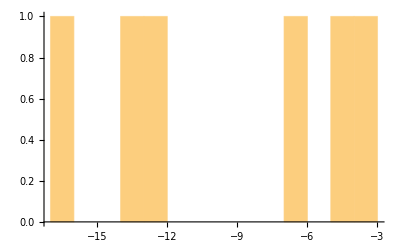

```mathematica
λ=2.00;
C0=Flatten[Select[activeLEC,#[[1]]==λ&]][[2]];
D1=Flatten[Select[activeLEC,#[[1]]==λ&]][[3]];

evlowthreshold=10^-10;
nbrW=25;
logspace[increments_,start_?Positive,end_?Positive]:=Exp@Range[Log@start,Log@end,Log[end/start]/increments];
gsEresults={};
gsEresultsB={};
SetSharedVariable[gsEresults,gsEresultsB];

ParallelDo[
dimD=17;
minWi=0.001;
maxWi=0.1+nn 1.43;
sigmi=15.0;
widths =Select[RandomVariate[NormalDistribution[maxWi,sigmi],dimD],#>0&];
dimD=Length[widths];

hamm=Table[ham[λ,widths[[i]],widths[[j]],C0,D1],{i,dimD},{j,dimD}];
normm=Table[norm[widths[[i]],widths[[j]]],{i,dimD},{j,dimD}];

normDiag=DiagonalMatrix[1./Sqrt[Diagonal[normm]]];
HamN=(Transpose[normDiag].hamm).normDiag;
NormN=(Transpose[normDiag].normm).normDiag;

esn=Eigensystem[NormN];
evBare=Sort[Eigenvalues[{hamm,normm}],Re[#1]<Re[#2]&];
AppendTo[gsEresultsB,evBare[[1]]];

{μ,transf}=Transpose[Select[Sort[Transpose[esn],#1[[1]]<#2[[1]]&],#[[1]]>evlowthreshold&]];
(*Print[Length[μ]];*)
trafma=(Transpose[transf].DiagonalMatrix[μ^(-1/2)]);
traham=(Transpose[trafma].HamN).trafma;
esh=Eigensystem[traham];
{ϵ,transfe}=Transpose[Sort[Transpose[esh],#1[[1]]<#2[[1]]&]];
gsh=transfe[[1,All]];
(*Print["E_0^(bare) = ",Sort[evBare][[1]]];*)
If[Select[ϵ,#<0&]≠{},
AppendTo[gsEresults,ϵ[[1]]]
(*Print["Dim - Dim_reduced = ",dimD," - ",Length[μ],"     0H0 = ",gsh.traham.gsh," =^! ",ϵ[[1]],"   E_0^(bare) = ",Sort[evBare][[;;4]]]*)
];
,{nn,Range[1,nbrW]}]
Sort[gsEresults,#1<#2&]
Histogram[gsEresults,{1}]
```

```mathematica
dimD=122;
maxWi=2.43;
sigmi=25.0;
widths =Select[RandomVariate[NormalDistribution[maxWi,sigmi],dimD],#>0&];
dimD=Length[widths];

hamm=Table[ham[λ,widths[[i]],widths[[j]],C0,D1],{i,dimD},{j,dimD}];
normm=Table[norm[widths[[i]],widths[[j]]],{i,dimD},{j,dimD}];

normm//MatrixForm;

normDiag=DiagonalMatrix[1./Sqrt[Diagonal[normm]]];
HamN=(Transpose[normDiag].hamm).normDiag;
NormN=(Transpose[normDiag].normm).normDiag;

NormN//MatrixForm;

esn=Eigensystem[NormN];
evBare=Sort[Eigenvalues[{hamm,normm}],Re[#1]<Re[#2]&];
evBareN=Sort[Eigenvalues[{HamN,NormN}],Re[#1]<Re[#2]&];

{μ,transf}=Transpose[Select[Sort[Transpose[esn],#1[[1]]<#2[[1]]&],#[[1]]>evlowthreshold&]];

trafma=(Transpose[transf].DiagonalMatrix[μ^(-1/2)]);
traham=(Transpose[trafma].HamN).trafma;
trano=(Transpose[trafma].NormN).trafma;

esh=Eigensystem[{traham,trano}];
{ϵ,transfe}=Transpose[Sort[Transpose[esh],#1[[1]]<#2[[1]]&]];
gsh=transfe[[1,All]];

{evBare[[1]],evBareN[[1]],ϵ[[1]]}
```

{-16779.5,ComplexInfinity,-150.654}

```mathematica
bnd=40;
ai=2;aj=1;lamm=1.4;
(* Subscript[δ, 12] Subscript[δ, 13] and Subscript[δ, 23] Subscript[δ, 13] and Subscript[δ, 12] Subscript[δ, 23] yield the same result *)
kernel3[x1_,x2_,b1_,b2_,la_]:=Exp[-2 (b1+b2) (x1^2+x2^2+x1 x2)-la ((x1-x2)^2+(x1-(-x1-x2))^2)];

nInt3=NIntegrate[kernel3[xa,xb,ai,aj,lamm],{xa,-bnd,bnd},{xb,-bnd,bnd}];
aInt3=(2 π)^3/((12 ((ai+aj)^2+3 lamm^2+4 lamm (ai+aj)))^(3/2));
Print["numerical:  ",nInt^3]
Print["analytical: ",N[aInt]]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

numerical:  nInt^3

analytical: aInt

```mathematica
kernel12[x1_,x2_,b1_,b2_,la_]:=Exp[-2 (b1+b2) (x1^2+x2^2+x1 x2)-la (x1-x2)^2];
kernel13[x1_,x2_,b1_,b2_,la_]:=Exp[-2 (b1+b2) (x1^2+x2^2+x1 x2)-la (2 x1+x2)^2];
kernel23[x1_,x2_,b1_,b2_,la_]:=Exp[-2 (b1+b2) (x1^2+x2^2+x1 x2)-la (x1+2 x2)^2];
nInt12=NIntegrate[kernel23[xa,xb,ai,aj,lamm],{xa,-bnd,bnd},{xb,-bnd,bnd}];
aInt12=(2 π)^3/((12 ((ai+aj)^2+2 lamm (ai+aj)))^(3/2));
Print["numerical:  ",nInt12^3]
Print["analytical: ",N[aInt12]]
```

numerical:  0.0822129

analytical: 0.0822136

```mathematica
Simplify[-2/3 (D[Exp[-b1 (x1^2+y1^2+z1^2+x2^2+y2^2+z2^2+(x1+x2)^2+(y1+y2)^2+(z1+z2)^2)],x1] D[Exp[-b2 (x1^2+y1^2+z1^2+x2^2+y2^2+z2^2+(x1+x2)^2+(y1+y2)^2+(z1+z2)^2)],x1]+D[Exp[-b1 (x1^2+y1^2+z1^2+x2^2+y2^2+z2^2+(x1+x2)^2+(y1+y2)^2+(z1+z2)^2)],y1] D[Exp[-b2 (x1^2+y1^2+z1^2+x2^2+y2^2+z2^2+(x1+x2)^2+(y1+y2)^2+(z1+z2)^2)],y1]+D[Exp[-b1 (x1^2+y1^2+z1^2+x2^2+y2^2+z2^2+(x1+x2)^2+(y1+y2)^2+(z1+z2)^2)],z1] D[Exp[-b2 (x1^2+y1^2+z1^2+x2^2+y2^2+z2^2+(x1+x2)^2+(y1+y2)^2+(z1+z2)^2)],z1]+D[Exp[-b1 (x1^2+y1^2+z1^2+x2^2+y2^2+z2^2+(x1+x2)^2+(y1+y2)^2+(z1+z2)^2)],x2] D[Exp[-b2 (x1^2+y1^2+z1^2+x2^2+y2^2+z2^2+(x1+x2)^2+(y1+y2)^2+(z1+z2)^2)],x2]+D[Exp[-b1 (x1^2+y1^2+z1^2+x2^2+y2^2+z2^2+(x1+x2)^2+(y1+y2)^2+(z1+z2)^2)],y2] D[Exp[-b2 (x1^2+y1^2+z1^2+x2^2+y2^2+z2^2+(x1+x2)^2+(y1+y2)^2+(z1+z2)^2)],y2]+D[Exp[-b1 (x1^2+y1^2+z1^2+x2^2+y2^2+z2^2+(x1+x2)^2+(y1+y2)^2+(z1+z2)^2)],z2] D[Exp[-b2 (x1^2+y1^2+z1^2+x2^2+y2^2+z2^2+(x1+x2)^2+(y1+y2)^2+(z1+z2)^2)],z2])
+1/3 (D[Exp[-b1 (x1^2+y1^2+z1^2+x2^2+y2^2+z2^2+(x1+x2)^2+(y1+y2)^2+(z1+z2)^2)],x1] D[Exp[-b2 (x1^2+y1^2+z1^2+x2^2+y2^2+z2^2+(x1+x2)^2+(y1+y2)^2+(z1+z2)^2)],x2]+D[Exp[-b1 (x1^2+y1^2+z1^2+x2^2+y2^2+z2^2+(x1+x2)^2+(y1+y2)^2+(z1+z2)^2)],y1] D[Exp[-b2 (x1^2+y1^2+z1^2+x2^2+y2^2+z2^2+(x1+x2)^2+(y1+y2)^2+(z1+z2)^2)],y2]+D[Exp[-b1 (x1^2+y1^2+z1^2+x2^2+y2^2+z2^2+(x1+x2)^2+(y1+y2)^2+(z1+z2)^2)],z1] D[Exp[-b2 (x1^2+y1^2+z1^2+x2^2+y2^2+z2^2+(x1+x2)^2+(y1+y2)^2+(z1+z2)^2)],z2]+D[Exp[-b1 (x1^2+y1^2+z1^2+x2^2+y2^2+z2^2+(x1+x2)^2+(y1+y2)^2+(z1+z2)^2)],x2] D[Exp[-b2 (x1^2+y1^2+z1^2+x2^2+y2^2+z2^2+(x1+x2)^2+(y1+y2)^2+(z1+z2)^2)],x1]+D[Exp[-b1 (x1^2+y1^2+z1^2+x2^2+y2^2+z2^2+(x1+x2)^2+(y1+y2)^2+(z1+z2)^2)],y2] D[Exp[-b2 (x1^2+y1^2+z1^2+x2^2+y2^2+z2^2+(x1+x2)^2+(y1+y2)^2+(z1+z2)^2)],y1]+D[Exp[-b1 (x1^2+y1^2+z1^2+x2^2+y2^2+z2^2+(x1+x2)^2+(y1+y2)^2+(z1+z2)^2)],z2] D[Exp[-b2 (x1^2+y1^2+z1^2+x2^2+y2^2+z2^2+(x1+x2)^2+(y1+y2)^2+(z1+z2)^2)],z1])]
```

ⅇ^(-17.2 x1^2-17.2 x1 x2-17.2 x2^2-17.2 y1^2-17.2 y1 y2-17.2 y2^2-17.2 z1^2-17.2 z1 z2-17.2 z2^2) (-138.24 x1^2-138.24 x1 x2-138.24 x2^2-138.24 y1^2-138.24 y1 y2-138.24 y2^2-138.24 z1^2-138.24 z1 z2-138.24 z2^2)

```mathematica
bnd=20;
ai=0.231;aj=1.33;
kernelT[x1_,x2_,y1_,y2_,z1_,z2_,b1_,b2_]:=-8 b1 b2 ⅇ^(-2 (b1+b2) (x1^2+x1 x2+x2^2+y1^2+y1 y2+y2^2+z1^2+z1 z2+z2^2)) (x1^2+x1 x2+x2^2+y1^2+y1 y2+y2^2+z1^2+z1 z2+z2^2);
nIntT=NIntegrate[kernelT[xa,xb,ya,yb,za,zb,ai,aj],{xa,-bnd,bnd},{xb,-bnd,bnd},{ya,-bnd,bnd},{yb,-bnd,bnd},{za,-bnd,bnd},{zb,-bnd,bnd}];
aIntT=((ai aj) (2 π)^3)/(2 3^(1/2)(ai+aj)^4);
Print["numerical:  ",nIntT]
Print["analytical: ",N[aIntT]]
nIntT/aIntT
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -3.70398 and 0.0166665 for the integral and error estimates.

numerical:  -3.70398

analytical: 3.70511

-0.999696

```mathematica
AMA={{4 (a1+a2)+10 λ,2 (a1+a2)+8 λ},{2 (a1+a2)+8 λ,4 (a1+a2)+10 λ}};
iAMA=Simplify[Inverse[AMA]];
AMA//MatrixForm
iAMA//MatrixForm
Simplify[Det[AMA]]
```

(40.+4 (a1+a2) | 32.+2 (a1+a2)
32.+2 (a1+a2) | 40.+4 (a1+a2))

((0.333333 (10.+a1+a2))/(48.+16. a1+a1^2+16. a2+2. a1 a2+a2^2) | (-2.66667-0.166667 a1-0.166667 a2)/(48.+16. a1+a1^2+16. a2+2. a1 a2+a2^2)
(-2.66667-0.166667 a1-0.166667 a2)/(48.+16. a1+a1^2+16. a2+2. a1 a2+a2^2) | (0.333333 (10.+a1+a2))/(48.+16. a1+a1^2+16. a2+2. a1 a2+a2^2))

12. (48.+a1^2+16. a2+a2^2+a1 (16.+2. a2))

```mathematica
AMA={{4 (a1+a2),2 (a1+a2)},{2 (a1+a2),4 (a1+a2)}};
iAMA=Simplify[Inverse[AMA]];
AMA//MatrixForm
iAMA//MatrixForm
Simplify[Det[AMA]]
```

(4 (a1+a2) | 2 (a1+a2)
2 (a1+a2) | 4 (a1+a2))

(1/(3 a1+3 a2) | -1/(6 (a1+a2))
-1/(6 (a1+a2)) | 1/(3 a1+3 a2))

12 (a1+a2)^2